```mathematica
EntityProperties["AdministrativeDivision"];
```

```mathematica
usstates=EntityList[EntityClass["AdministrativeDivision","ContinentalUSStates"]];
```

```mathematica
EntityValue[category[[1]],"Definition"]
```

```mathematica
category2=Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Educational"]&][[1]]
```

```mathematica
GeoRegionValuePlot[usstates->category2,ColorFunctionScaling->True]
```

```mathematica
(* 
annual births-deaths-population - health insurance - "civilian unemployment rate", employment - "uninsured population fraction" "people with/out health insurance "home ownership rate""   "home vacancy rate"
"infant deaths" "minimum wage" "per capita income" "population by poverty status" "population density" "position"
*)
```

```mathematica
(* annual deaths / population = % of people per state who die every year *)
```

```mathematica
(* people without health insurance / population = % of people who do not have health insurance *)
```

```mathematica
(* other stuff that may be interesting from the above list *)
```

```mathematica
(* Preliminary for CE: *)
```

```mathematica
populationentity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Population"]&][[1]]
```

population

```mathematica
populationvalue = value=EntityValue[usstates,populationentity];
```

```mathematica
deathsentity=  Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Deaths"]&][[1]]
```

annual deaths

```mathematica
deathsvalue = value=EntityValue[usstates,deathsentity]/populationvalue//Normalize;
```

```mathematica
nohientity = Select[EntityProperties["AdministrativeDivision"],StringContainsQ[CanonicalName[#], "Insurance"]&][[3]]
```

people without health insurance

```mathematica
nohivalue = value=EntityValue[usstates,nohientity]/populationvalue//Normalize;
```

```mathematica
data = Table[{usstates[[i]],nohivalue[[i]],deathsvalue[[i]]},{i,Length[usstates]}];
```

```mathematica
data[[All,3]]//N//Sort//Reverse
```

{0.194042,0.173927,0.166295,0.166016,0.165507,0.164961,0.16463,0.16363,0.162804,0.161116,0.159599,0.158064,0.155979,0.15495,0.154496,0.152015,0.151889,0.148754,0.147588,0.146685,0.144482,0.144061,0.141243,0.140254,0.137888,0.137875,0.137646,0.137602,0.137437,0.136431,0.135599,0.135342,0.134496,0.133739,0.133583,0.133393,0.130822,0.130787,0.130185,0.129444,0.129134,0.128713,0.123089,0.122744,0.116231,0.113674,0.112502,0.090674}

```mathematica
badfit = Fit[data[[All,2;;]],{1,x},x]
```

0.142079+0.00783509 x

```mathematica
plt1=ListPlot[data[[All,2;;3]],PlotRange->All];
```

```mathematica
plt2 = Plot[badfit,{x,Min[data[[All,2]]],Max[data[[All,2]]]}];
```

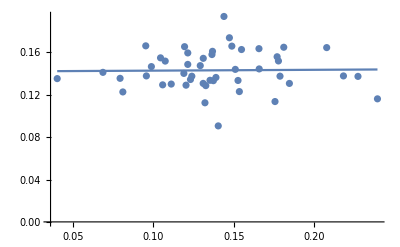

```mathematica
Show[plt1,plt2]
```

```mathematica
(* Ignore from here *)
```

```mathematica
Correlation[deathsvalue,nohivalue]
```

0.0168384

```mathematica
(* Choose some other quantities, create correlation plots *)
```